```mathematica
(* MA39110 / Assignment 11 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
cnt=0;max=0;
Model[n0_,r0_]:=Module[{n=n0,r=r0},
x0=0;xf=1;h=(xf-x0)/n;
X=Table[x0+x*h,{x,1,n-1}];
XT=Table[x0+x*h,{x,0,n}];
f[x_]=Sin[Pi*x];
U=Table[f[XT[[x]]],{x,1,n+1}];
UT=U;
UTT=UT;
PLT=Table[0,{x,1,100}];
For[j=1,j≤100,j++,{
U=UT;
For[i=1,i<n,i++,
{
im=i+1;
If[j≠1,UT[[im]]=r*U[[im-1]]+2(1-r)U[[im]]+r*U[[im+1]]-UTT[[im]],UT[[im]]=(1/2)(r*U[[im-1]]+2(1-r)U[[im]]+r*U[[im+1]])];
}];
UTT=UT;
PLT[[j]]=ListLinePlot[Transpose[{XT,UT}],PlotRange->Full];
}];
Show[{PLT[[1;;;;10]]},PlotLabel->Style[StringForm["h = ``, k = ``",h,h*Sqrt[r]],FontSize->10]]
];
```

```mathematica
(*GraphicsGrid[{{Model[10,0.5],Model[10,0.1]},{Model[20,0.5],Model[20,0.1]}}]*)
```

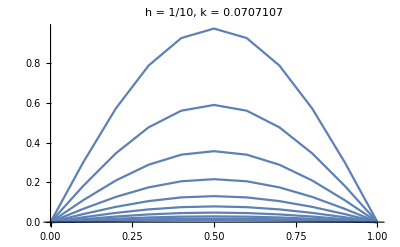

```mathematica
Model[10,0.5]
```